# Beam Shaping

## Last Updated: 12/27/2022

```mathematica
Quit[];
```

```mathematica
(*Remove["Global`*"];ClearInOut[];*)
```

## Prep

## Plotting Setup

```mathematica
SetOptions[Plot,ImageSize->Large,PlotRange->Full];
SetOptions[ListPlot,ImageSize->Large,PlotRange->Full];
```

```mathematica
Off[General::munfl];
```

## Global Variables

### Units

```mathematica
inch=2.54*^-2;
cm=1*^-2;mm=1*^-3;um=1*^-6;nm=1*^-9;
```

## Gaussian Beams

```mathematica
(*q[z_,b_]+z2_^:=q[z+z2,b]*)
```

### ABCD Matrices

#### Base ABCD Matrices

```mathematica
mFree[l_]:={{1,l},{0,1}};
```

```mathematica
mLens[f_]:={{1,0},{-1/f,1}};
```

```mathematica
mMirror[f_]:={{1,0},{-1/f,1}};
```

```mathematica
mFace[R_,n1_,n2_]:={{1,0},{(n1-n2)/(n2*R),n1/n2}};
```

#### Composite ABCD Matrices

```mathematica
mTelescope[f1_,f2_]=Simplify[mLens[f2].mFree[f1+f2].mLens[f1]];
```

```mathematica
mFiberCoupler[f_]=Simplify[mFree[f].mLens[f]];
```

### Beam Properties

```mathematica
BeamWaist[q[z_,b_],λ_:λ0]:=√((λ*b)/π*(1+(z/b)^2));
```

```mathematica
BeamRadius[q[z_,b_]]:=z+b^2/z;
```

```mathematica
BeamAngle[q[z_,b_],λ_:λ0]:=ArcTan[√(λ/(π*b))];
```

```mathematica
GouyPhase[q[z_,b_]]:=π/2+Arg[z+ⅈ*b]
```

### Efficiency

```mathematica
ApertureEfficiency[q[z_,b_],w_]:=Integrate[Exp[-2(x/#)^2],{x,-w,w}]/(#√(π/2))&[BeamWaist[q[z,b]]];
```

```mathematica
FiberEfficiency[q[z_,b_],w_,d_]:=2/(π*w*#)*(Integrate[Exp[-((x/#)^2+(x/w)^2)],{x,-d,d}])^2&[BeamWaist[q[z,b]]];
```

```mathematica
clipTMP=2*Integrate[√(2/(π*w^2))Exp[-2 x^2/w^2],{x,w1,∞}];
TrapClipping[wTMP_,w1TMP_]:=Evaluate[clipTMP]/.{w->wTMP,w1->w1TMP}//N;
```

## OOP

```mathematica
(*todo: could instead do oop by making matrices dot q?*)
```

### Legacy

```mathematica
(*mDJ_[q[z_,b_]]^:=(mDJ[[1,1]]*(z+ⅈ*b)+mDJ[[1,2]])/(mDJ[[2,1]]*(z+ⅈ*b)+mDJ[[2,2]]);*)
```

```mathematica
(*mDJ_List[q_Complex]:=(mDJ[[1,1]]*q+mDJ[[1,2]])/(mDJ[[2,1]]*q+mDJ[[2,2]])*)
(*mCore[q_Complex]:=(mCore[[1,1]]*q+mCore[[1,2]])/(mCore[[2,1]]*q+mCore[[2,2]]);*)
```

### Matrix on q

```mathematica
mDJ_List[q[z_,b_]]^:=Simplify[q[Re[#],Im[#]]&[(mDJ[[1,1]]*(z+ⅈ*b)+mDJ[[1,2]])/(mDJ[[2,1]]*(z+ⅈ*b)+mDJ[[2,2]])],{z∈Reals,b∈Reals}];
```

## QOL

### Optimize Collimation Lens Placement

```mathematica
(*
get qx and qy;
get placement region;
get end position;
get beam waist range;
scan y position for each x (get waist propagation after end of placement region);
get residuals squared divided by range;
sort by minimum of residuals squared
*)
```

```mathematica
(*todo: parallelize*)
```

```mathematica
(*f[x1_,y1_]:=*)
```

```mathematica
(*Map[Apply[x1^2+y1^2/.{x1->#1,y1->#2},#]&,{{1,1},{2,2},{3,3}}]*)
```

```mathematica
OptimizeCollimation[q0_List,fx_,fy_,placement_List,endPos_]:=Module[
{zArr=Range[placement[[2]],endPos,5mm]//N,z,
posArr=Subsets[Range[placement[[1]],placement[[2]]-(fy[[1]]+fy[[2]]),2mm],{2}]//N,
waistX,waistXArr,x1,
waistY,waistYArr,y1,
collimateVal,collimateValArr,result
},
waistX=BeamWaist[(mFree[z].mFree[placement[[2]]-x1].mLens[fx].mFree[x1])[q0[[1]]]];
waistY=BeamWaist[(mFree[z].mFree[placement[[2]]-(y1+fy[[1]]+fy[[2]])].mTelescope[fy[[1]],fy[[2]]].mFree[y1])[q0[[2]]]];
collimateVal=ComplexExpand[Total[(waistX-waistY)^2/.{z->#}&/@zArr]]//Chop;
collimateValArr=MapThread[collimateVal/.{x1->#1,y1->#2}&,posArr//Transpose]//Chop;
result=Sort[AssociationThread[posArr->collimateValArr]];
Return[result];
];
```

## Plotting

### Beam Plot

```mathematica
PlotWaist[q[z_,b_],params_,points_:100]:=With[
{funcDJ=BeamWaist[q[z+params[[1]],b]]},
ListPlot[(funcDJ/um/.{params[[1]]->#})&/@Range[params[[2]],params[[3]],(params[[3]]-params[[2]])/points],DataRange->{params[[2]],params[[3]]}/mm,AxesLabel->{"Position (mm)","Beam Waist (um)"},ImageSize->Large,PlotLabel->"Start Waist: "<>ToString[#1]<>"um; End Waist: "<>ToString[#2]<>"um"&[funcDJ/um/.{params[[1]]->params[[2]]},funcDJ/um/.{params[[1]]->params[[3]]}]]
];
```

```mathematica
GetPoints[q[z_,b_],params_,points_:100]:=With[
{funcDJ=BeamWaist[q[z+params[[1]],b]]},
(funcDJ/um/.{params[[1]]->#})&/@Range[params[[2]],params[[3]],(params[[3]]-params[[2]])/points]
];
```

### Summary of Beampath

```mathematica
SummarizePath[q[z0_,b0_],elements_Association,endPos:(_Real|_Rational|_Integer)]:=Module[
{elements2=KeySort[elements],
distFreePos=#[[2;;]]-#[[;;-2]]&[Sort[Join[Keys[elements],{0,N[endPos]}]]],
distFreeMat,
matDJ,
BeamExprArr,
z,
data},
distFreeMat=mFree[#]&/@distFreePos;
matDJ=MapThread[Dot[#1,#2]&,{Values[elements2],distFreeMat[[;;-2]]}];
matDJ=FoldList[#2.#1&,IdentityMatrix[2],matDJ];
BeamExprArr=Simplify[BeamWaist[(mFree[z].#)[q[z0,b0]]]]&/@matDJ;
data=Table[BeamExprArr[[i]]/.{z->#}&/@Range[0,distFreePos[[i]],0.1mm],{i,Length[BeamExprArr]}];
Return[data];
];
```

```mathematica
(*
association of elements and positions;
sort elements by position;
get points from position to position;
return beamwaists at each position;
concatenate points and plot while noting each position;
*)
```

## Lens Placement

## 393nm

```mathematica
λ0=393*nm;
```

```mathematica
z0x=-3.315;w0x=318*um;q0x=q[z0x,(π*w0x^2)/λ0];
```

```mathematica
z0y=-1.41;w0y=472*um;q0y=q[z0y,(π*w0y^2)/λ0];
```

### Calculate Path

```mathematica
endPoint=1010.83mm;
```

```mathematica
targetPoints={131.24mm,375.71mm,1010.83mm};
```

```mathematica
xPath={150mm->mLens[150mm],344mm->mLens[50mm]};
yPath={};
```

#### Plot

```mathematica
(*create path*)
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

```mathematica
(*get waist values*)
targetWaists={xSummary[[IntegerPart[#/mm*10]]]/um,ySummary[[IntegerPart[#/mm*10]]]/um}&/@targetPoints;
```

```mathematica
(*create summary plots for x- and y- directions*)
{xSummaryPlot,ySummaryPlot}=ListPlot[
#/um,
ImageSize->Large,
DataRange->{0,Length[#]/10},
AxesLabel->{"Position (mm)","Beam Waist (μm)"},
GridLines->{targetPoints/mm,{}}
]&/@{xSummary,ySummary};
```

```mathematica
(*combine plots*)
summaryPlot=ListPlot[
#/um,
ImageSize->Large,
DataRange->{0,Max[Length/@#]/10},
AxesLabel->{"Position (mm)","Beam Waist (μm)"},
PlotLabels->{"x","y"},
GridLines->{targetPoints/mm,{}}
]&[{xSummary,ySummary}];
```

#### Show

```mathematica
{
MatrixForm[targetWaists],
summaryPlot
}
```

{(1292.23 | 581.095
448.809 | 545.841
437.935 | 483.718),-Graphics-}

## 397nm

```mathematica
λ0=397*nm;
```

```mathematica
z0x=-0.73;w0x=130*um;q0x=q[z0x,(π*w0x^2)/λ0];
```

```mathematica
z0y=-0.21;w0y=250*um;q0y=q[z0y,(π*w0y^2)/λ0];
```

### Fix Astigmatism

```mathematica
region1End=500mm;
```

#### Cylindrical Lens Parameters

```mathematica
f1x=-500*mm;
f1y=20*mm;f2y=40*mm;
```

```mathematica
xLens1Pos=(Abs[z0x]-Abs[f1x])+20mm
yLens1Pos=(*Abs[z0y]-0mm*)270mm//N
```

0.25

0.27

#### Propagate

{q[0.476554,1.82847],q[0.29,1.97833]}

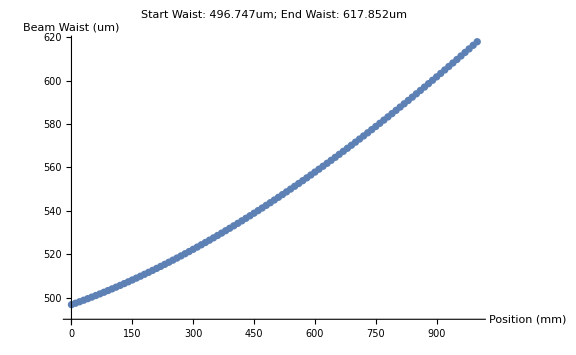
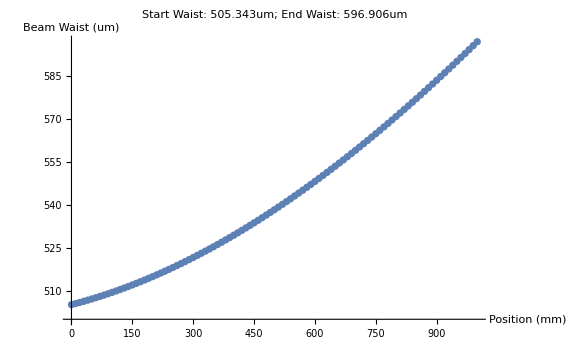

```mathematica
mCollimateX=mFree[region1End-xLens1Pos].mLens[f1x].mFree[xLens1Pos];
mCollimateY=mFree[region1End-(yLens1Pos+f1y+f2y)].mTelescope[f1y,f2y].mFree[yLens1Pos];
{qDJx,qDJy}={mCollimateX[q0x],mCollimateY[q0y]}
PlotWaist[#,{z,0mm,1000*mm}]&/@{qDJx,qDJy}
```

#### Optimized Propagate

```mathematica
AbsoluteTiming[OP1=OptimizeCollimation[{q0x,q0y},f1x,{f1y,f2y},{100mm,420mm},1000mm];]
OP1[[;;10]]
```

$Aborted

Part::take: Cannot take positions 1 through 10 in OP1.

OP1⟦1;;10⟧

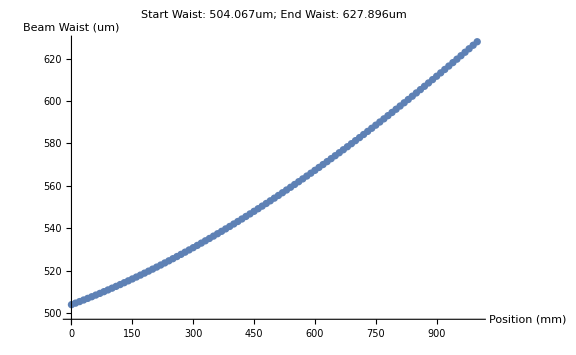
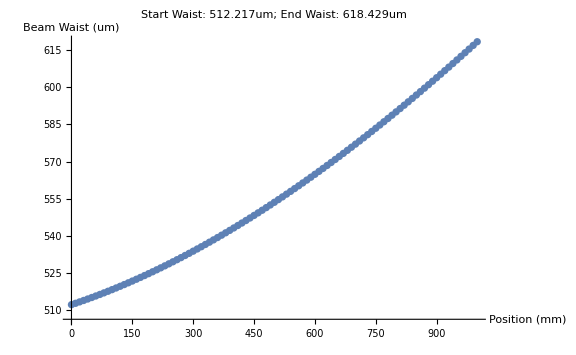

```mathematica
Lens1Pos=0.242;yLens1Pos=0.35;
mOptimalCollimateX=mFree[Clip[(yLens1Pos+f1y+f2y)-xLens1Pos,{0,∞}]].mLens[f1x].mFree[xLens1Pos];
mOptimalCollimateY=mFree[Clip[xLens1Pos-(yLens1Pos+f1y+f2y),{0,∞}]].mTelescope[f1y,f2y].mFree[yLens1Pos];
qOptimalCollimate={mOptimalCollimateX[q0x],mOptimalCollimateY[q0y]};
PlotWaist[#,{z,0mm,1000*mm}]&/@qOptimalCollimate
```

### Beam Down Through AOM

```mathematica
region2Start=550mm;
region2End=1000mm;
```

```mathematica
AOM1HeadPos=650mm;(*AOM1HeadPos=543.92mm;*)
{q1x1,q1y1}=mFree[region2Start-region1End][#]&/@{qDJx,qDJy};
```

```mathematica
AOM2HeadPos=700mm;(*AOM2HeadPos=632.87mm;*)
{q1x2,q1y2}=mFree[region2Start-region1End][#]&/@{qDJx,qDJy};
```

#### AOM & Lens Parameters

```mathematica
AOMWaist=175um;AOMLength=24.51mm;
```

```mathematica
f1AOM1=150 mm;f2AOM1=50mm;
```

#### AOM1 Entrance

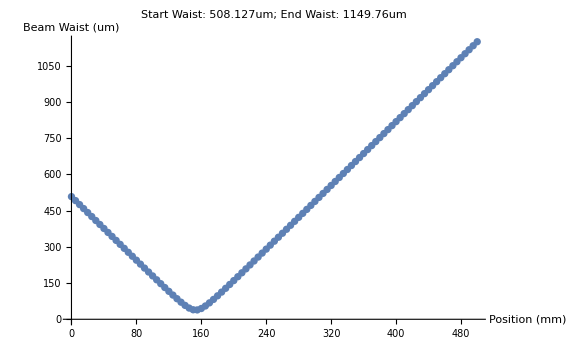
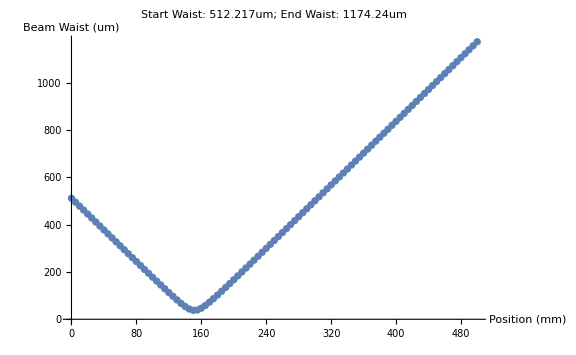

```mathematica
mAOM1=mLens[f1AOM1].mFree[AOM1HeadPos-region2Start];
{qDJx1,qDJy1}=mAOM1[#]&/@{q1x1,q1y1};
PlotWaist[#,{z,0,500mm}]&/@{qDJx1,qDJy1}
```

```mathematica
Print["AOM Beam Angle (rad): ",BeamAngle[#]&/@{qDJx1,qDJy1}];
Print["AOM Entrance Efficiency: ",100*(Times@@(ApertureEfficiency[#,AOMWaist]&/@{qDJx1,qDJx1}))," %"];
```

AOM Beam Angle (rad): {0.00331163,0.00336894}

AOM Entrance Efficiency: 25.9135 %

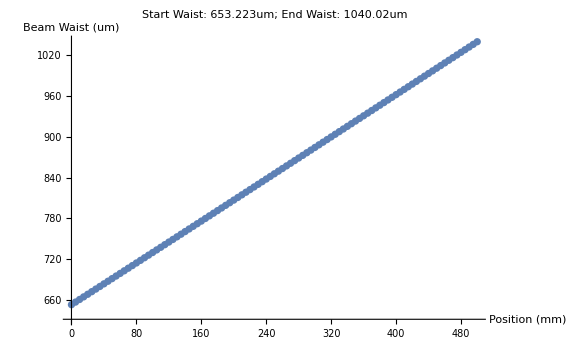
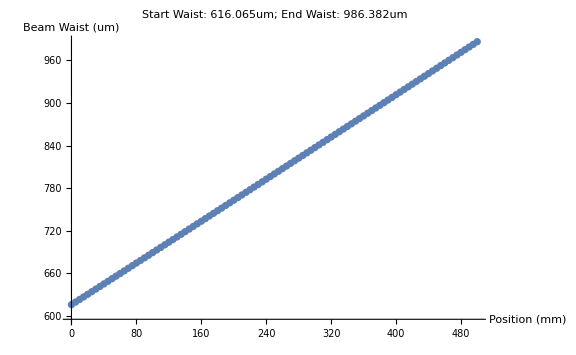

```mathematica
mOut=mFree[region2End-(f1AOM1+f2AOM1)].mLens[f2AOM1].mFree[f1AOM1+f2AOM1];
PlotWaist[mOut[#],{z,0,500mm}]&/@{qDJx1,qDJy1}
```

#### AOM2 Entrance

```mathematica
mLens2AOM2X=mLens2SingleX.mFree[88.95mm];
mLens2AOM2Y=mLens2SingleX.mFree[88.95mm];
{qAOM2x,qAOM2y}={mLens2AOM2X[qDJx],mLens2AOM2X[qDJy]};
```

{180.027,174.481}

{0.948123,0.955138}

0.905588

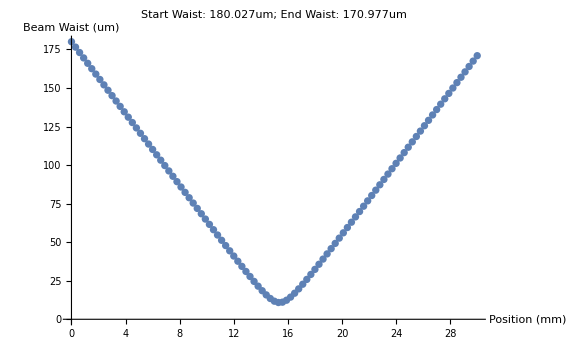
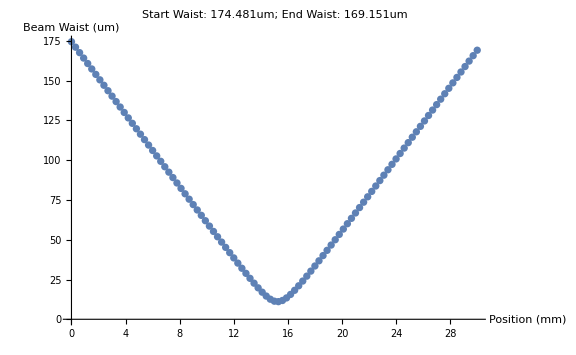

```mathematica
BeamWaist[#]/um&/@{qAOM2x,qAOM2y}
ApertureEfficiency[#,175um]&/@{qAOM2x,qAOM2y}
Times@@%
PlotWaist[#,{z,0,30*mm}]&/@{qAOM2x,qAOM2y}
```

### Into Fibers

#### Fiber Coupler Parameters

```mathematica
fCoupler=4.6mm;wCoupler=375um;mfdCoupler=3.5um/2;
```

```mathematica
fiberRadius=1.5um;wFiber=1um;
```

#### Wavemeter Fiber

```mathematica
wavemeterFiberPos=973.11mm;
```

```mathematica
xDiffPos=wavemeterFiberPos-region1End;
```

```mathematica
mWavemeterX=mFiberCoupler[fCoupler].mFree[(wavemeterFiberPos-fCoupler)-xLens1Pos];
mWavemeterY=mFiberCoupler[fCoupler].mFree[(wavemeterFiberPos-fCoupler)-(yLens1Pos+f1y+f2y)];
{qWMx,qWMy}={mWavemeterX[qDJx],mWavemeterY[qDJy]}
```

{q[-5.15922×10^-6,8.09417×10^-6],q[-3.66307×10^-6,9.24439×10^-6]}

{1.19934,1.1626}

{0.873874,0.87007}

0.760332

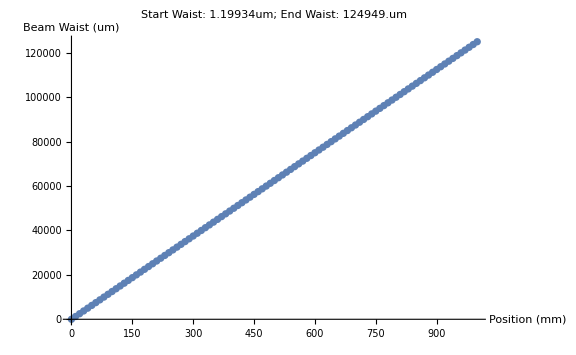
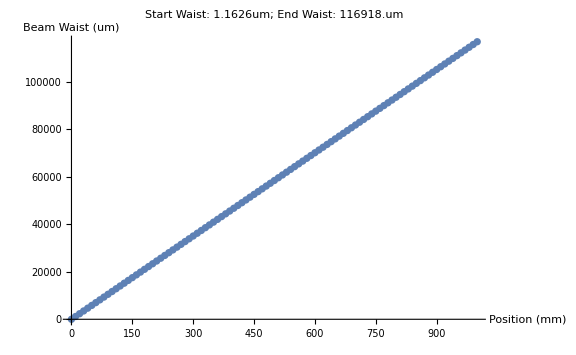

```mathematica
BeamWaist[#]/um&/@{qWMx,qWMy}
FiberEfficiency[#,mfdCoupler,fiberRadius]&/@{qWMx,qWMy}
Times@@%
PlotWaist[#,{z,0mm,1000*mm}]&/@{qWMx,qWMy}
```

#### AOM1 Fiber

```mathematica
region2EndAOM1=region1End+f21+f22;
AOM1FiberPos=1250.59mm;
```

```mathematica
mFinal=mFiberCoupler[fCoupler].mFree[(AOM1FiberPos-fCoupler)-region2EndAOM1];
{qFiber1x1,qFiber1y1}={mFinal[qAOM1x2],mFinal[qAOM1y2]};
```

{1.59912,1.55013}

{0.877021,0.89007}

0.78061

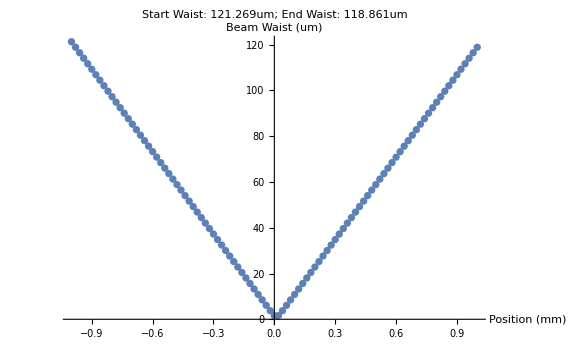
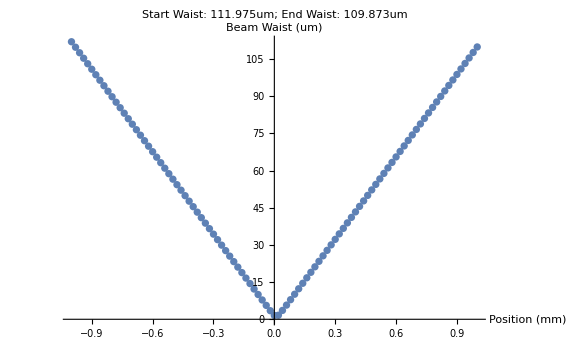

```mathematica
BeamWaist[#]/um&/@{qFiber1x1,qFiber1y1}
FiberEfficiency[#,wFiber,fiberRadius]&/@{qFiber1x1,qFiber1y1}
Times@@%
PlotWaist[#,{z,-1mm,1mm}]&/@{qFiber1x1,qFiber1y1}
```

#### AOM2 Fiber

```mathematica
AOM1FiberPos=1172.39mm;
```

### Summary

#### Calculate Path

```mathematica
endPoint=1500mm;
```

```mathematica
xPath={250mm->mLens[-500mm],650mm->mLens[200mm],950mm->mLens[100mm]};
yPath={270mm->mLens[20mm],330mm->mLens[40mm],650mm->mLens[200mm],950mm->mLens[100mm]};
```

```mathematica
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

#### Plot

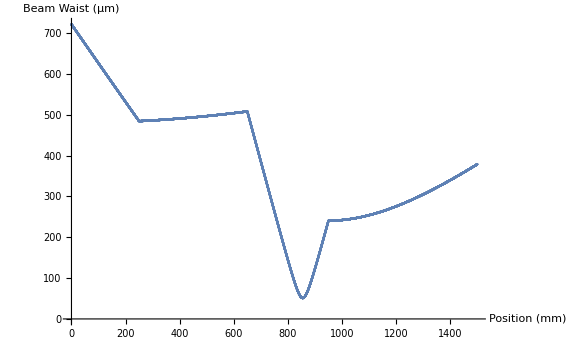
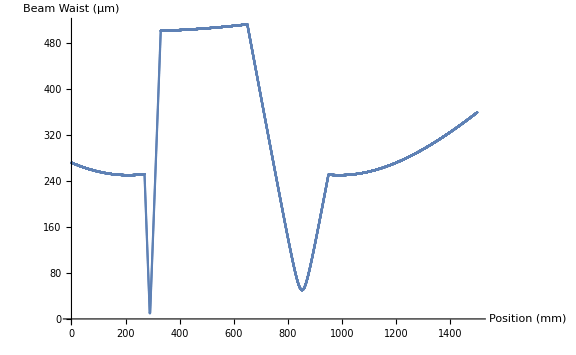

-Graphics-

```mathematica
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"}]&/@{xSummary,ySummary}
ListPlot[{xSummary,ySummary}/um,ImageSize->Large,DataRange->{0,Max[Length/@{xSummary,ySummary}]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"}]
```

## 423nm

```mathematica
λ0=423*nm;
```

```mathematica
z0x=-0.71;w0x=120*um;q0x=q[z0x,(π*w0x^2)/λ0];
```

```mathematica
z0y=-0.50;w0y=272*um;q0y=q[z0y,(π*w0y^2)/λ0];
```

### Fix Astigmatism

```mathematica
region1End=900mm;
```

#### Cylindrical Lens Parameters

```mathematica
f1x=-500*mm;
f1y=20*mm;f2y=40*mm;
```

```mathematica
xLens1Pos=(Abs[z0x]-Abs[f1x])+25mm
yLens1Pos=Abs[z0y]+100mm//N
```

0.235

0.6

#### Propagate

{q[0.64688,2.21647],q[0.52,2.1979]}

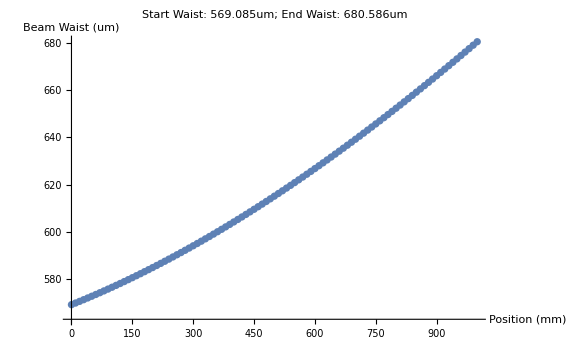
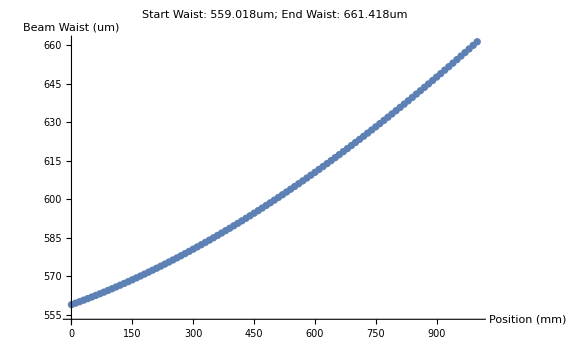

```mathematica
mCollimateX=mFree[region1End-xLens1Pos].mLens[f1x].mFree[xLens1Pos];
mCollimateY=mFree[region1End-(yLens1Pos+f1y+f2y)].mTelescope[f1y,f2y].mFree[yLens1Pos];
{qDJx,qDJy}={mCollimateX[q0x],mCollimateY[q0y]}
PlotWaist[#,{z,0mm,1000*mm}]&/@{qDJx,qDJy}
```

#### Optimized Propagate

```mathematica
(*AbsoluteTiming[OP1=OptimizeCollimation[{q0x,q0y},f1x,{f1y,f2y},{25mm,400mm},1000mm];]
OP1[[;;10]]*)
```

```mathematica
(*Lens1Pos=0.15;yLens1Pos=0.32;
mOptimalCollimateX=mFree[Clip[(yLens1Pos+f1y+f2y)-xLens1Pos,{0,∞}]].mLens[f1x].mFree[xLens1Pos];
mOptimalCollimateY=mFree[Clip[xLens1Pos-(yLens1Pos+f1y+f2y),{0,∞}]].mTelescope[f1y,f2y].mFree[yLens1Pos];
qOptimalCollimate={mOptimalCollimateX[q0x],mOptimalCollimateY[q0y]};
PlotWaist[#,{z,0mm,1000*mm}]&/@qOptimalCollimate*)
```

### Beam Down Through AOM

```mathematica
region2Start=550mm;
region2End=1000mm;
```

```mathematica
AOM1HeadPos=650mm;(*AOM1HeadPos=543.92mm;*)
{q1x1,q1y1}=mFree[region2Start-region1End][#]&/@{qDJx,qDJy};
```

```mathematica
AOM2HeadPos=700mm;(*AOM2HeadPos=632.87mm;*)
{q1x2,q1y2}=mFree[region2Start-region1End][#]&/@{qDJx,qDJy};
```

#### AOM & Lens Parameters

```mathematica
AOMWaist=175um;AOMLength=24.51mm;
```

```mathematica
f1AOM1=150 mm;f2AOM1=50mm;
```

#### AOM1 Entrance

```mathematica
mAOM1=mLens[f1AOM1].mFree[AOM1HeadPos-region2Start];
{qDJx1,qDJy1}=mAOM1[#]&/@{q1x1,q1y1};
PlotWaist[#,{z,0,500mm}]&/@{qDJx1,qDJy1}
```

{-Graphics-,-Graphics-}

```mathematica
Print["AOM Beam Angle (rad): ",BeamAngle[#]&/@{qDJx1,qDJy1}];
Print["AOM Entrance Efficiency: ",100*(Times@@(ApertureEfficiency[#,AOMWaist]&/@{qDJx1,qDJx1}))," %"];
```

AOM Beam Angle (rad): {0.00331163,0.00336894}

AOM Entrance Efficiency: 25.9135 %

```mathematica
mOut=mFree[region2End-(f1AOM1+f2AOM1)].mLens[f2AOM1].mFree[f1AOM1+f2AOM1];
PlotWaist[mOut[#],{z,0,500mm}]&/@{qDJx1,qDJy1}
```

{-Graphics-,-Graphics-}

#### AOM2 Entrance

```mathematica
mLens2AOM2X=mLens2SingleX.mFree[88.95mm];
mLens2AOM2Y=mLens2SingleX.mFree[88.95mm];
{qAOM2x,qAOM2y}={mLens2AOM2X[qDJx],mLens2AOM2X[qDJy]};
```

```mathematica
BeamWaist[#]/um&/@{qAOM2x,qAOM2y}
ApertureEfficiency[#,175um]&/@{qAOM2x,qAOM2y}
Times@@%
PlotWaist[#,{z,0,30*mm}]&/@{qAOM2x,qAOM2y}
```

{180.027,174.481}

{0.948123,0.955138}

0.905588

{-Graphics-,-Graphics-}

### Into Fibers

### Summary

#### Calculate Path

```mathematica
endPoint=1650mm;
```

```mathematica
xPath={235mm->mLens[-500mm],1050mm->mLens[250mm],1225mm->mLens[-75mm]};
yPath={600mm->mLens[20mm],660mm->mLens[40mm],1050mm->mLens[250mm],1225mm->mLens[-75mm]};
```

```mathematica
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

#### Plot

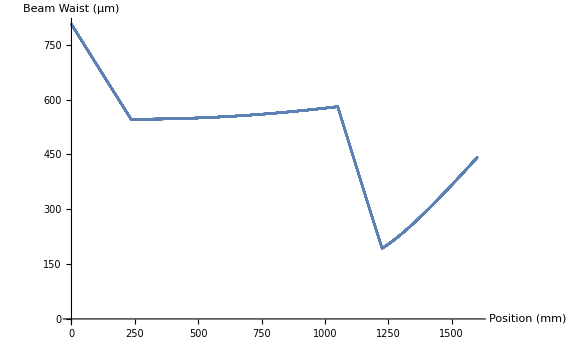
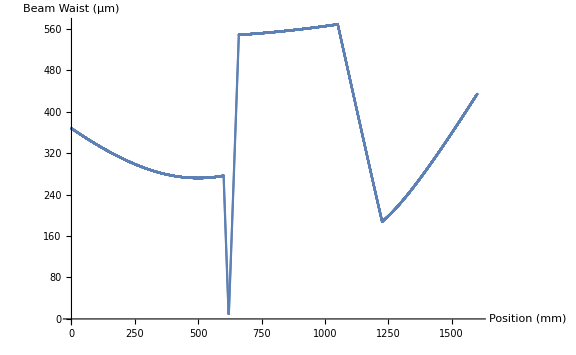

-Graphics-

```mathematica
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"}]&/@{xSummary,ySummary}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Max[Length/@#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"}]&[{xSummary,ySummary}]
```

## 849nm

```mathematica
λ0=854*nm;
z0x=-7.1;w0x=1380*um;q0x=q[z0x,(π*w0x^2)/λ0];
z0y=0.27;w0y=510*um;q0y=q[z0y,(π*w0y^2)/λ0];
```

### Summary

#### Calculate Path

```mathematica
endPoint=1300mm;(*28 to split, 16 to main*)
```

```mathematica
xPath={325mm->mLens[40mm],385mm->mLens[20mm]};
yPath={150mm->mLens[1000mm]};
```

```mathematica
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

#### Plot

```mathematica
ListPlot[{xSummary,ySummary}/um,ImageSize->Large,DataRange->{0,Max[Length/@{xSummary,ySummary}]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"}]
```

-Graphics-

## 854nm

```mathematica
λ0=854*nm;
z0x=3.3;w0x=600*um;q0x=q[z0x,(π*w0x^2)/λ0];
z0y=0.96;w0y=470*um;q0y=q[z0y,(π*w0y^2)/λ0];
```

### Summary

#### Calculate Path

```mathematica
endPoint=1300mm;(*28 to split, 16 to main*)
```

```mathematica
xPath={325mm->mLens[40mm],385mm->mLens[20mm]};
yPath={150mm->mLens[1000mm]};
```

```mathematica
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

#### Plot

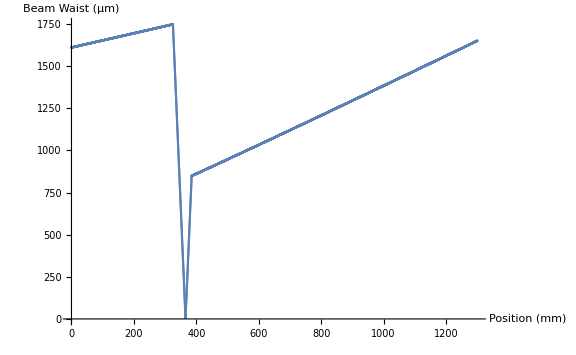
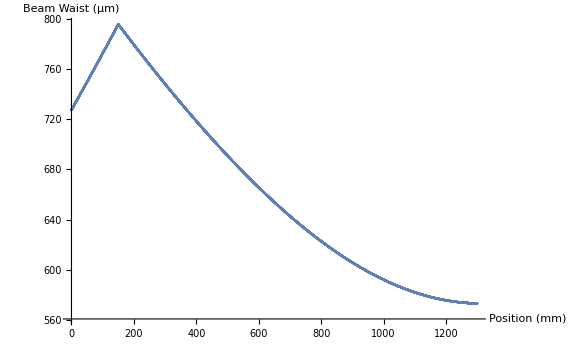

-Graphics-

```mathematica
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"}]&/@{xSummary,ySummary}
ListPlot[{xSummary,ySummary}/um,ImageSize->Large,DataRange->{0,Max[Length/@{xSummary,ySummary}]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"}]
```

## 866nm

```mathematica
λ0=866*nm;
```

```mathematica
z0x=-5.0;w0x=1300*um;q0x=q[z0x,(π*w0x^2)/λ0];
```

```mathematica
z0y=0.438;w0y=475*um;q0y=q[z0y,(π*w0y^2)/λ0];
```

### Fix Astigmatism

```mathematica
region1End=500mm;
```

#### Cylindrical Lens Parameters

```mathematica
f1x=40*mm;f2x=20mm;
fColY=500mm;
f1y=40*mm;f2y=60*mm;
```

```mathematica
xLens1Pos=100mm;
yLens1Pos=fColY-Abs[z0y]+100mm;yLens2Pos=yLens1Pos+200mm;
```

#### Propagate

{q[-0.915,1.53271],q[-1.11973,0.677125]}

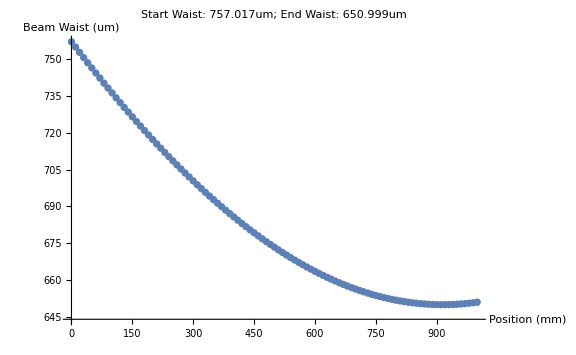
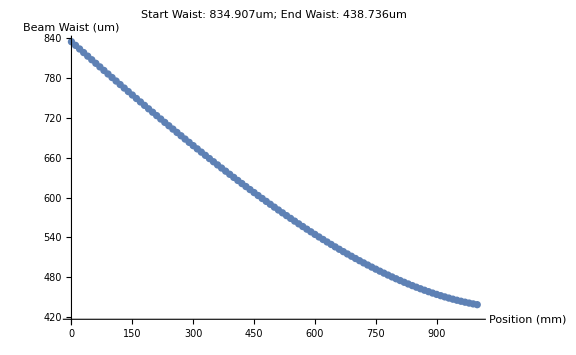

```mathematica
mCollimateX=mFree[region1End-(xLens1Pos+f1x+f2x)].mTelescope[f1x,f2x].mFree[xLens1Pos];
mCollimateY=mFree[region1End-(yLens1Pos+f1y+f2y)].mTelescope[f1y,f2y].mLens[fColY].mFree[yLens1Pos];
{qDJx,qDJy}={mCollimateX[q0x],mCollimateY[q0y]}
PlotWaist[#,{z,0mm,1000*mm}]&/@{qDJx,qDJy}
```

### Beam Down Through AOM

```mathematica
(*region2Start=550mm;
region2End=1000mm;*)
```

```mathematica
(*AOM1HeadPos=650mm;(*AOM1HeadPos=543.92mm;*)
{q1x1,q1y1}=mFree[region2Start-region1End][#]&/@{qDJx,qDJy};*)
```

```mathematica
(*AOM2HeadPos=700mm;(*AOM2HeadPos=632.87mm;*)
{q1x2,q1y2}=mFree[region2Start-region1End][#]&/@{qDJx,qDJy};*)
```

#### AOM & Lens Parameters

```mathematica
(*AOMWaist=175um;AOMLength=24.51mm;*)
```

```mathematica
(*f1AOM1=150 mm;f2AOM1=50mm;*)
```

#### AOM1 Entrance

```mathematica
(*mAOM1=mLens[f1AOM1].mFree[AOM1HeadPos-region2Start];
{qDJx1,qDJy1}=mAOM1[#]&/@{q1x1,q1y1};
PlotWaist[#,{z,0,500mm}]&/@{qDJx1,qDJy1}*)
```

```mathematica
(*Print["AOM Beam Angle (rad): ",BeamAngle[#]&/@{qDJx1,qDJy1}];
Print["AOM Entrance Efficiency: ",100*(Times@@(ApertureEfficiency[#,AOMWaist]&/@{qDJx1,qDJx1}))," %"];*)
```

```mathematica
(*mOut=mFree[region2End-(f1AOM1+f2AOM1)].mLens[f2AOM1].mFree[f1AOM1+f2AOM1];
PlotWaist[mOut[#],{z,0,500mm}]&/@{qDJx1,qDJy1}*)
```

#### AOM2 Entrance

```mathematica
(*mLens2AOM2X=mLens2SingleX.mFree[88.95mm];
mLens2AOM2Y=mLens2SingleX.mFree[88.95mm];
{qAOM2x,qAOM2y}={mLens2AOM2X[qDJx],mLens2AOM2X[qDJy]};*)
```

```mathematica
(*BeamWaist[#]/um&/@{qAOM2x,qAOM2y}
ApertureEfficiency[#,175um]&/@{qAOM2x,qAOM2y}
Times@@%
PlotWaist[#,{z,0,30*mm}]&/@{qAOM2x,qAOM2y}*)
```

### Summary

#### Calculate Path

```mathematica
endPoint=2000mm;
```

```mathematica
(*xPath={xLens1Pos->mLens[40mm],xLens1Pos+60mm->mLens[20mm]};*)
(*yPath={yLens1Pos->mLens[500mm],yLens2Pos->mLens[40mm],yLens2Pos+100mm->mLens[60mm]};*)
(*xPath={0->mLens[60mm],0+80mm->mLens[20mm]};
yPath={62mm->mLens[1000mm]};*)
xPath={300mm->mLens[60mm],300mm+80mm->mLens[20mm]};
yPath={62mm->mLens[500mm],500mm->mLens[40mm],600mm->mLens[60mm]};
```

```mathematica
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

#### Plot

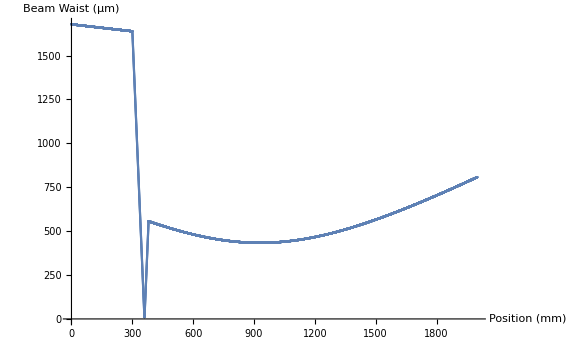
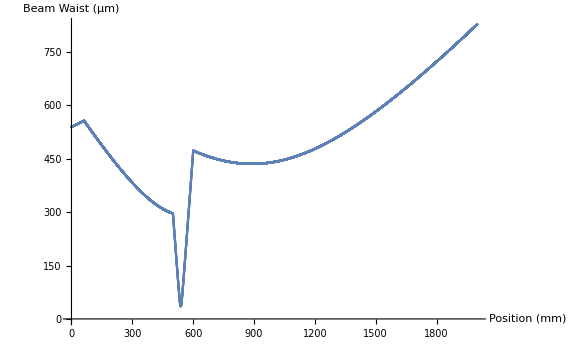

-Graphics-

```mathematica
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"}]&/@{xSummary,ySummary}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Max[Length/@#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"}]&[{xSummary,ySummary}]
```

## Breadboard Beam Shaping

## Clipping

```mathematica
(*trap width in vertical direction*)
r0TRAP=0.55/(√2)mm;
```

```mathematica
beamWaists={150*um,200*um,250*um,300*um};
TrapClipping[#,r0TRAP]*100&/@beamWaists
```

{0.0000215494,0.0100622,0.186285,0.952189}

```mathematica
(*b-parameter*)
(π*(150um)^2)/(400*nm)//N
```

0.176715

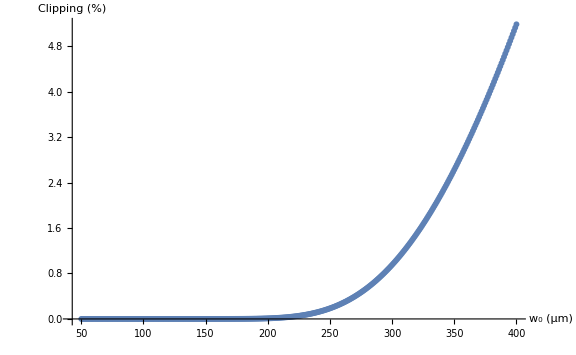

```mathematica
(*plot clipping as a function of beam waist*)
w0Arr=Range[50um,400um,1um];
clipSweep=TrapClipping[#,r0TRAP]*100&/@w0Arr;
ListPlot[clipSweep,DataRange->w0Arr[[{1,-1}]]/um,AxesLabel->{"w_0 (μm)","Clipping (%)"}]
```

## 243nm

```mathematica
λ0=243*nm;
```

```mathematica
w0=1mm;
q0x=q[0,(π*w0^2)/λ0];q0y=q[0,(π*w0^2)/λ0];
```

### Calculate Path

```mathematica
(*~7'=2150mm before bb, 260 shape region on bb, 360mm from bb to trap center*)
endPoint=3000mm;targetPoint=2750mm;(*~5' table to table*)
```

```mathematica
xPath={1300mm->mLens[500mm],1900mm->mLens[100mm]};
yPath={2300mm->mLens[500mm]};
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

#### Plot

{362.488,113.369}

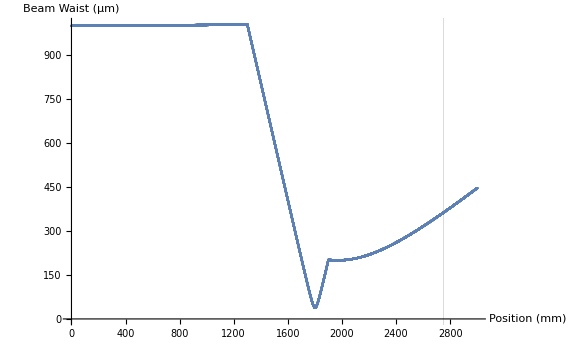
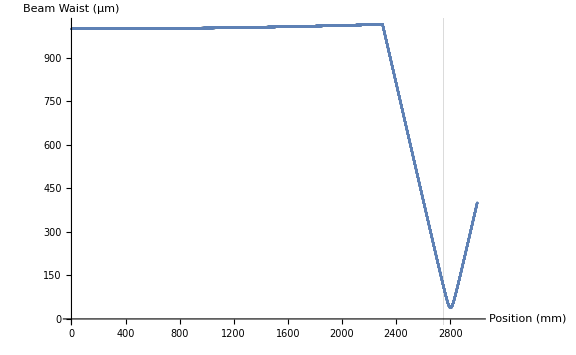

-Graphics-

```mathematica
{xSummary[[targetPoint/mm*10]]/um,ySummary[[targetPoint/mm*10]]/um}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},GridLines->{{targetPoint/mm},{}}]&/@{xSummary,ySummary}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Max[Length/@#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"},GridLines->{{targetPoint/mm},{}}]&[{xSummary,ySummary}]
```

## 397nm

```mathematica
λ0=397*nm;
```

```mathematica
w0=1.1um;
q0x=q[0,(π*w0^2)/λ0];q0y=q[0,(π*w0^2)/λ0];
```

### Calculate Path

```mathematica
endPoint=1500mm;targetPoint=1170mm;(*th: 22" or 560mm to first coupler*)
```

```mathematica
xPath={4.57mm->mLens[4.6mm],500mm->mLens[400mm]};
yPath={4.6mm->mLens[4.6mm]};
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

#### Plot

{130.763,596.898}

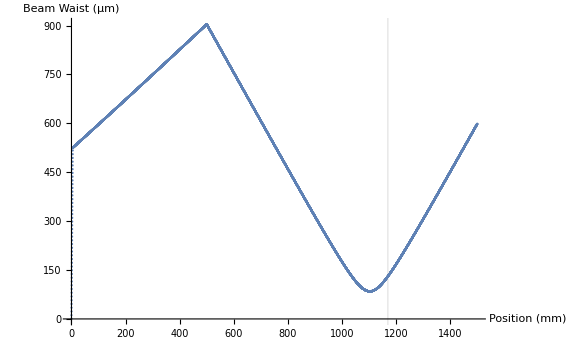
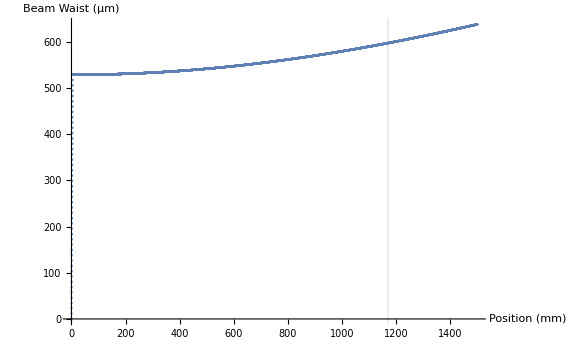

-Graphics-

```mathematica
{xSummary[[targetPoint/mm*10]]/um,ySummary[[targetPoint/mm*10]]/um}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},GridLines->{{targetPoint/mm},{}}]&/@{xSummary,ySummary}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Max[Length/@#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"},GridLines->{{targetPoint/mm},{}}]&[{xSummary,ySummary}]
```

## 423/375nm

```mathematica
yzde1={{1,0},{0,1/1.5}};yzde2={{1,0},{0,1.5}};
```

```mathematica
λ0=423*nm;
w0=1.1um/350*423;
q0x=q[0,(π*w0^2)/λ0];q0y=q[0,(π*w0^2)/λ0];
```

```mathematica
λ1=375*nm;
w1x=226um;w1y=84um;
q1x=q[-630mm,(π*w1x^2)/λ1];q1y=q[-720mm,(π*w1y^2)/λ1];
```

### Calculate Path

```mathematica
endPoint=800mm;targetPoint=640mm;(*th: 22" or 560mm to first coupler*)
```

```mathematica
xPath={4.55mm->mLens[4.6mm],50mm->mLens[250mm]};
yPath={4.55mm->mLens[4.6mm],50mm->mLens[250mm],400mm->yzde1,405mm->yzde2,450mm->yzde1,455mm->yzde2};
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

```mathematica
x1Path={450mm->mLens[250mm]};
y1Path=x1Path;
x1Summary=SummarizePath[q1x,Association[x1Path],endPoint]//Flatten;
y1Summary=SummarizePath[q1y,Association[y1Path],endPoint]//Flatten;
```

#### Plot

{160.851,159.03}

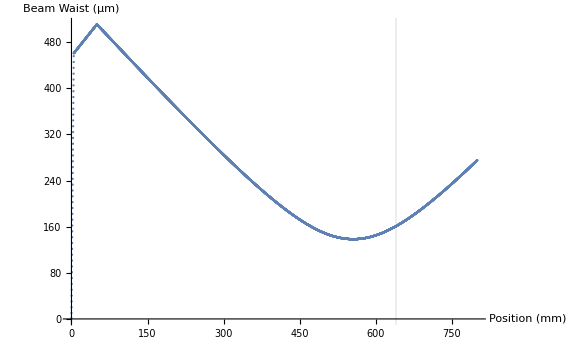
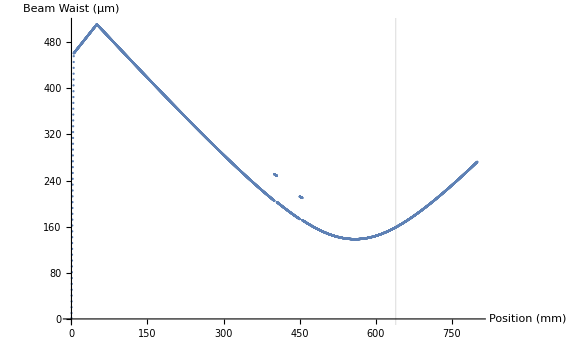

-Graphics-

```mathematica
{xSummary[[targetPoint/mm*10]]/um,ySummary[[targetPoint/mm*10]]/um}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},GridLines->{{targetPoint/mm},{}}]&/@{xSummary,ySummary}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Max[Length/@#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"},GridLines->{{targetPoint/mm},{}}]&[{xSummary,ySummary}]
(*
{x1Summary[[targetPoint/mm*10]]/um,y1Summary[[targetPoint/mm*10]]/um}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},GridLines->{{targetPoint/mm},{}}]&/@{x1Summary,y1Summary}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Max[Length/@#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"},GridLines->{{targetPoint/mm},{}}]&[{x1Summary,y1Summary}]*)
```

## 729nm

```mathematica
λ0=729*nm;
```

```mathematica
w0=2.60*um;
q0x=q[0,(π*w0^2)/λ0];q0y=q[0,(π*w0^2)/λ0];
```

### Calculate Path

```mathematica
(*
	0-178mm: beam-shaping region;
	178mm-283mm: coupling region;
	283mm-481mm: final breadboard region;
	695.6mm: trap center
*)
endPoint=1000mm;
targetPoint=695.6mm;
```

```mathematica
xPath={4.53mm->mLens[4.6mm],175mm->mLens[250mm]};
yPath={4.6mm->mLens[4.6mm]};
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

#### Plot

{193.678,564.781}

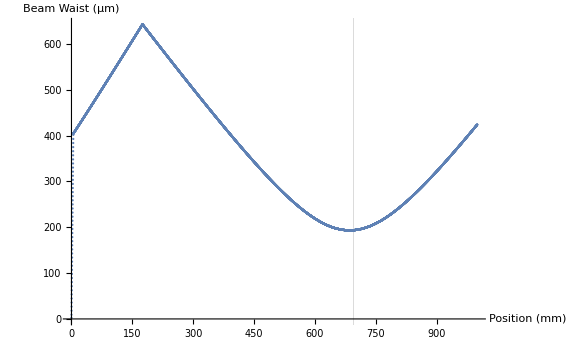
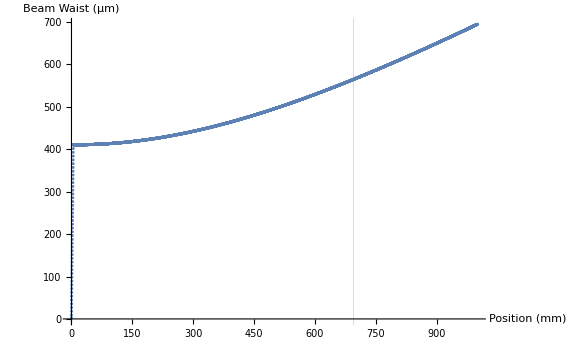

-Graphics-

```mathematica
{xSummary[[targetPoint/mm*10]]/um,ySummary[[targetPoint/mm*10]]/um}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},GridLines->{{targetPoint/mm},{}}]&/@{xSummary,ySummary}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Max[Length/@#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"},GridLines->{{targetPoint/mm},{}}]&[{xSummary,ySummary}]
```

## 854nm

```mathematica
λ0=854*nm;
w0=2.5um;
q0x=q[0,(π*w0^2)/λ0];q0y=q[0,(π*w0^2)/λ0];
```

### Calculate Path

```mathematica
endPoint=2500mm;targetPoint=1460mm;
```

```mathematica
xPath={4.56mm->mLens[4.6mm],600mm->mLens[300mm](*500mm->mLens[500mm],1151mm->mLens[150mm]*)};
yPath={4.62mm->mLens[4.6mm](*,800mm->mLens[150mm],1140mm->mLens[63.6mm]*)};
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

#### Plot

{1170.28,809.923}

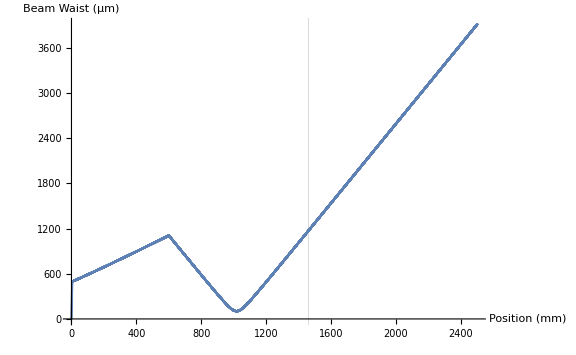
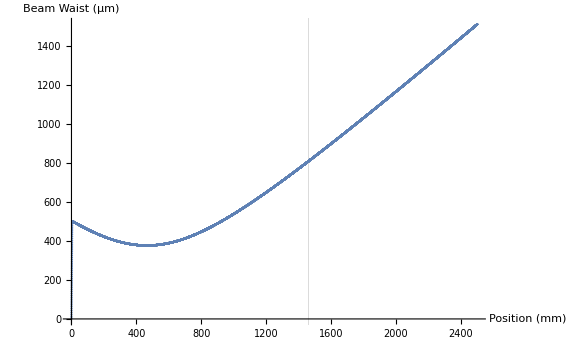

-Graphics-

```mathematica
{xSummary[[targetPoint/mm*10]]/um,ySummary[[targetPoint/mm*10]]/um}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},GridLines->{{targetPoint/mm},{}}]&/@{xSummary,ySummary}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Max[Length/@#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"},GridLines->{{targetPoint/mm},{}}]&[{xSummary,ySummary}]
```

## 3800nm

```mathematica
λ0=3800*nm;
```

```mathematica
w0=1mm;
q0x=q[0,(π*w0^2)/λ0];q0y=q[0,(π*w0^2)/λ0];
```

### Calculate Path

```mathematica
(*
	0-260mm: beam-shaping region;
	260mm-360mm: coupling region;
	360mm-490mm: final breadboard region;
	680mm: trap center
*)
endPoint=1000mm;
targetPoint=680mm;
```

```mathematica
xPath={250mm->mLens[450mm]};
yPath={};
xSummary=SummarizePath[q0x,Association[xPath],endPoint]//Flatten;
ySummary=SummarizePath[q0y,Association[yPath],endPoint]//Flatten;
```

#### Plot

{535.336,1294.73}

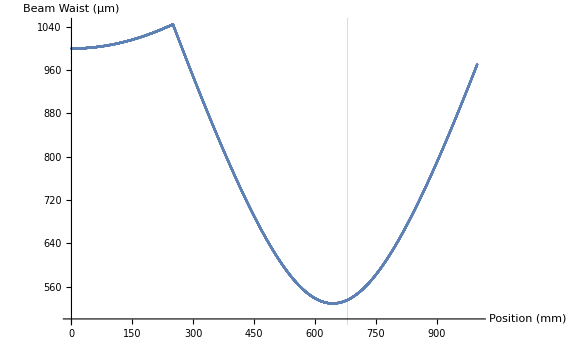
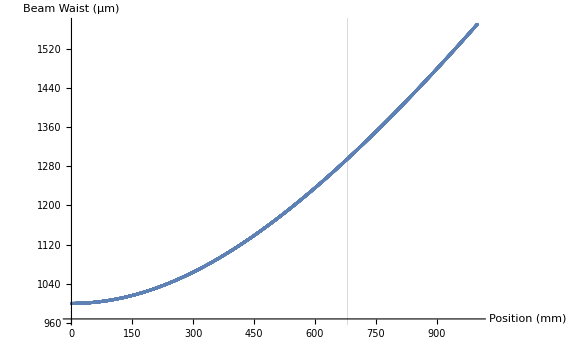

-Graphics-

```mathematica
{xSummary[[targetPoint/mm*10]]/um,ySummary[[targetPoint/mm*10]]/um}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Length[#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},GridLines->{{targetPoint/mm},{}}]&/@{xSummary,ySummary}
ListPlot[#/um,ImageSize->Large,DataRange->{0,Max[Length/@#]/10},AxesLabel->{"Position (mm)","Beam Waist (μm)"},PlotLabels->{"x","y"},GridLines->{{targetPoint/mm},{}}]&[{xSummary,ySummary}]
```

## Other